# Pango analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/pango-countries

```mathematica
dataset="pango-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

```mathematica
gridCount=1;
```

## Setup

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01","2022-08-01","2022-09-01","2022-10-01","2022-11-01"};
```

### Countries

```mathematica
countriesToDrop={};
```

## Variants and colors

### Import

```mathematica
variantData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=variantData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
variantData=Drop[variantData,1];
```

```mathematica
variants=Union[variantData[[All,3]]]
```

{BA.2.3.20,BA.2.75,BA.2.75.2,BA.4.1,BA.4.6,BA.4.6.5,BA.5,BA.5.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.2,BA.5.1.22,BA.5.1.23,BA.5.1.27,BA.5.1.30,BA.5.1.5,BA.5.1.6,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.20,BA.5.2.21,BA.5.2.23,BA.5.2.31,BA.5.2.34,BA.5.2.6,BA.5.2.9,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.6,BA.5.9,BE.1,BE.1.1,BE.1.1.1,BE.1.2,BE.1.2.1,BE.1.4,BF.10,BF.11,BF.13,BF.14,BF.26,BF.32,BF.5,BF.7,BF.7.4,BF.7.4.1,BN.1,BN.1.3,BN.1.3.1,BQ.1,BQ.1.1,BQ.1.10,BQ.1.10.1,BQ.1.11,BQ.1.1.18,BQ.1.12,BQ.1.1.3,BQ.1.13,BQ.1.1.4,BQ.1.14,BQ.1.1.5,BQ.1.1.7,BQ.1.2,BQ.1.22,BQ.1.3,BQ.1.5,BQ.1.6,CK.1,other,XBB,XBB.1}

```mathematica
n=Length[variants]
```

75

### Max frequency

```mathematica
variantFrequencyMapping=Table[variant->Max[Cases[variantData,x_/;x[[3]]==variant][[All,11]]],{variant,variants}];
```

```mathematica
highFrequencyVariants=Cases[variantFrequencyMapping,x_/;x[[2]]>=0.005][[All,1]];
```

```mathematica
Length[highFrequencyVariants]
```

62

```mathematica
lowFrequencyVariants=Complement[variants,highFrequencyVariants];
```

```mathematica
Length[lowFrequencyVariants]
```

13

```mathematica
variants=Join[highFrequencyVariants,lowFrequencyVariants];
```

```mathematica
n=Length[variants]
```

75

### Variant to clade mapping and clade colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.05;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
variantToClade=Map[#[[1]]->#[[2]]&,Drop[Import["../../data/pango-countries/pango_aliasing.tsv"],1]];
```

```mathematica
clades={"other","21L (Omicron)","22A (Omicron)","22B (Omicron)","22C (Omicron)","22D (Omicron)","22E (Omicron)","22F (Omicron)"};
```

```mathematica
cladeColors=Prepend[makeColors[Length[clades]-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.54357188, 0.73433536, 0.41441192],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
cladeToColor=MapThread[#1->#2&,{clades,cladeColors}]
```

{other→GrayLevel[0.5],21L (Omicron)→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],22A (Omicron)→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],22B (Omicron)→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],22C (Omicron)→RGBColor[0.54357188, 0.73433536, 0.41441192],22D (Omicron)→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],22E (Omicron)→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

### Colors

```mathematica
colorMappingForClade[clade_]:=Module[{pos,shades,tints,col},
pos=Flatten[Position[variants,x_/;(x/.variantToClade)==clade]];
If[Length[pos]>0,
shades=Reverse[Table[Darker[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}]];
tints=Drop[Table[Lighter[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}],1];
col=Join[shades,tints];
Table[variants[[pos[[i]]]]->col[[i]],{i,Length[pos]}],
{}
]
]
```

```mathematica
variantColorMapping=Flatten[Map[colorMappingForClade,clades]]
```

{other→RGBColor[0.5, 0.5, 0.5],BA.2.3.20→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],BA.4.1→RGBColor[0.16722636444444447, 0.2664698311111111, 0.5412847555555556],BA.4.6→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],BA.4.6.5→RGBColor[0.5005596977777778, 0.5998031644444444, 0.8746180888888889],BA.5→RGBColor[0.17903980977777778, 0.3284696376296296, 0.33898617125925934],BA.5.1→RGBColor[0.18682414933333333, 0.3427509262222222, 0.3537247004444445],BA.5.1.1→RGBColor[0.1946084888888889, 0.3570322148148148, 0.3684632296296297],BA.5.1.10→RGBColor[0.20239282844444445, 0.3713135034074074, 0.3832017588148149],BA.5.1.18→RGBColor[0.210177168, 0.38559479199999996, 0.39794028800000003],BA.5.1.2→RGBColor[0.21796150755555554, 0.3998760805925926, 0.41267881718518523],BA.5.1.22→RGBColor[0.2257458471111111, 0.41415736918518514, 0.42741734637037043],BA.5.1.23→RGBColor[0.23353018666666667, 0.4284386577777778, 0.44215587555555563],BA.5.1.27→RGBColor[0.24131452622222221, 0.4427199463703704, 0.45689440474074083],BA.5.1.30→RGBColor[0.2490988657777778, 0.45700123496296297, 0.471632933925926],BA.5.1.5→RGBColor[0.2568832053333333, 0.47128252355555555, 0.4863714631111112],BA.5.2→RGBColor[0.2646675448888889, 0.48556381214814814, 0.5011099922962964],BA.5.2.1→RGBColor[0.27245188444444446, 0.49984510074074073, 0.5158485214814815],BA.5.2.20→RGBColor[0.280236224, 0.5141263893333333, 0.5305870506666668],BA.5.2.21→RGBColor[0.28802056355555555, 0.5284076779259259, 0.5453255798518519],BA.5.2.23→RGBColor[0.2958049031111111, 0.5426889665185185, 0.5600641090370371],BA.5.2.34→RGBColor[0.30358924266666665, 0.5569702551111111, 0.5748026382222223],BA.5.2.6→RGBColor[0.3113735822222222, 0.5712515437037037, 0.5895411674074075],BA.5.2.9→RGBColor[0.31915792177777774, 0.5855328322962963, 0.6042796965925926],BA.5.3.1→RGBColor[0.3269422613333333, 0.5998141208888889, 0.6190182257777779],BA.5.5→RGBColor[0.3347266008888889, 0.6140954094814814, 0.633756754962963],BA.5.5.1→RGBColor[0.3425109404444444, 0.628376698074074, 0.6484952841481483],BA.5.6→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],BE.1→RGBColor[0.36473316266666667, 0.6505989202962963, 0.6707175063703704],BE.1.1→RGBColor[0.37917104533333335, 0.6585398539259258, 0.6782011994074075],BF.10→RGBColor[0.39360892799999997, 0.6664807875555555, 0.6856848924444445],BF.11→RGBColor[0.40804681066666665, 0.6744217211851852, 0.6931685854814815],BF.13→RGBColor[0.4224846933333333, 0.6823626548148147, 0.7006522785185186],BF.26→RGBColor[0.436922576, 0.6903035884444444, 0.7081359715555556],BF.5→RGBColor[0.45136045866666663, 0.6982445220740741, 0.7156196645925926],BF.7→RGBColor[0.4657983413333333, 0.7061854557037037, 0.7231033576296297],BF.7.4→RGBColor[0.480236224, 0.7141263893333333, 0.7305870506666667],BF.7.4.1→RGBColor[0.49467410666666667, 0.7220673229629629, 0.7380707437037037],CK.1→RGBColor[0.5091119893333333, 0.7300082565925925, 0.7455544367407408],BA.5.1.12→RGBColor[0.523549872, 0.7379491902222222, 0.7530381297777778],BA.5.1.6→RGBColor[0.5379877546666667, 0.7458901238518518, 0.7605218228148148],BA.5.2.16→RGBColor[0.5524256373333334, 0.7538310574814815, 0.768005515851852],BA.5.2.31→RGBColor[0.56686352, 0.761771991111111, 0.775489208888889],BA.5.9→RGBColor[0.5813014026666666, 0.7697129247407407, 0.782972901925926],BE.1.1.1→RGBColor[0.5957392853333333, 0.7776538583703704, 0.790456594962963],BE.1.2→RGBColor[0.610177168, 0.7855947919999999, 0.797940288],BE.1.2.1→RGBColor[0.6246150506666667, 0.7935357256296296, 0.805423981037037],BE.1.4→RGBColor[0.6390529333333332, 0.8014766592592593, 0.8129076740740742],BF.14→RGBColor[0.6534908159999999, 0.8094175928888889, 0.8203913671111112],BF.32→RGBColor[0.6679286986666666, 0.8173585265185185, 0.8278750601481482],BA.2.75→RGBColor[0.4674202559999999, 0.43492383199999995, 0.160484552],BA.2.75.2→RGBColor[0.623227008, 0.5798984426666667, 0.21397940266666668],BN.1→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],BN.1.3→RGBColor[0.8232270079999999, 0.7798984426666666, 0.41397940266666666],BN.1.3.1→RGBColor[0.867420256, 0.834923832, 0.560484552],BQ.1→RGBColor[0.4508135, 0.26993600000000006, 0.10418300000000001],BQ.1.1→RGBColor[0.5009038888888888, 0.29992888888888897, 0.11575888888888891],BQ.1.10→RGBColor[0.5509942777777778, 0.32992177777777787, 0.1273347777777778],BQ.1.11→RGBColor[0.6010846666666667, 0.35991466666666677, 0.13891066666666668],BQ.1.1.18→RGBColor[0.6511750555555555, 0.3899075555555557, 0.15048655555555557],BQ.1.12→RGBColor[0.7012654444444444, 0.4199004444444445, 0.16206244444444445],BQ.1.1.3→RGBColor[0.7513558333333333, 0.4498933333333335, 0.17363833333333334],BQ.1.13→RGBColor[0.8014462222222222, 0.4798862222222223, 0.18521422222222225],BQ.1.1.4→RGBColor[0.8515366111111111, 0.5098791111111113, 0.19679011111111114],BQ.1.14→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],BQ.1.1.5→RGBColor[0.9070921666666666, 0.5654346666666668, 0.2523456666666667],BQ.1.1.7→RGBColor[0.9125573333333333, 0.5909973333333335, 0.29632533333333333],BQ.1.2→RGBColor[0.9180225, 0.6165600000000001, 0.34030499999999997],BQ.1.22→RGBColor[0.9234876666666666, 0.6421226666666667, 0.38428466666666666],BQ.1.3→RGBColor[0.9289528333333333, 0.6676853333333335, 0.42826433333333336],BQ.1.5→RGBColor[0.934418, 0.6932480000000001, 0.472244],BQ.1.10.1→RGBColor[0.9398831666666666, 0.7188106666666667, 0.5162236666666666],BQ.1.6→RGBColor[0.9453483333333333, 0.7443733333333333, 0.5602033333333333],XBB→RGBColor[0.43033934, 0.07852116000000002, 0.06833224],XBB.1→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
highFrequencyColors=highFrequencyVariants/.variantColorMapping
```

{RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.4674202559999999, 0.43492383199999995, 0.160484552],RGBColor[0.623227008, 0.5798984426666667, 0.21397940266666668],RGBColor[0.16722636444444447, 0.2664698311111111, 0.5412847555555556],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.5005596977777778, 0.5998031644444444, 0.8746180888888889],RGBColor[0.17903980977777778, 0.3284696376296296, 0.33898617125925934],RGBColor[0.18682414933333333, 0.3427509262222222, 0.3537247004444445],RGBColor[0.1946084888888889, 0.3570322148148148, 0.3684632296296297],RGBColor[0.20239282844444445, 0.3713135034074074, 0.3832017588148149],RGBColor[0.210177168, 0.38559479199999996, 0.39794028800000003],RGBColor[0.21796150755555554, 0.3998760805925926, 0.41267881718518523],RGBColor[0.2257458471111111, 0.41415736918518514, 0.42741734637037043],RGBColor[0.23353018666666667, 0.4284386577777778, 0.44215587555555563],RGBColor[0.24131452622222221, 0.4427199463703704, 0.45689440474074083],RGBColor[0.2490988657777778, 0.45700123496296297, 0.471632933925926],RGBColor[0.2568832053333333, 0.47128252355555555, 0.4863714631111112],RGBColor[0.2646675448888889, 0.48556381214814814, 0.5011099922962964],RGBColor[0.27245188444444446, 0.49984510074074073, 0.5158485214814815],RGBColor[0.280236224, 0.5141263893333333, 0.5305870506666668],RGBColor[0.28802056355555555, 0.5284076779259259, 0.5453255798518519],RGBColor[0.2958049031111111, 0.5426889665185185, 0.5600641090370371],RGBColor[0.30358924266666665, 0.5569702551111111, 0.5748026382222223],RGBColor[0.3113735822222222, 0.5712515437037037, 0.5895411674074075],RGBColor[0.31915792177777774, 0.5855328322962963, 0.6042796965925926],RGBColor[0.3269422613333333, 0.5998141208888889, 0.6190182257777779],RGBColor[0.3347266008888889, 0.6140954094814814, 0.633756754962963],RGBColor[0.3425109404444444, 0.628376698074074, 0.6484952841481483],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.36473316266666667, 0.6505989202962963, 0.6707175063703704],RGBColor[0.37917104533333335, 0.6585398539259258, 0.6782011994074075],RGBColor[0.39360892799999997, 0.6664807875555555, 0.6856848924444445],RGBColor[0.40804681066666665, 0.6744217211851852, 0.6931685854814815],RGBColor[0.4224846933333333, 0.6823626548148147, 0.7006522785185186],RGBColor[0.436922576, 0.6903035884444444, 0.7081359715555556],RGBColor[0.45136045866666663, 0.6982445220740741, 0.7156196645925926],RGBColor[0.4657983413333333, 0.7061854557037037, 0.7231033576296297],RGBColor[0.480236224, 0.7141263893333333, 0.7305870506666667],RGBColor[0.49467410666666667, 0.7220673229629629, 0.7380707437037037],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.8232270079999999, 0.7798984426666666, 0.41397940266666666],RGBColor[0.867420256, 0.834923832, 0.560484552],RGBColor[0.4508135, 0.26993600000000006, 0.10418300000000001],RGBColor[0.5009038888888888, 0.29992888888888897, 0.11575888888888891],RGBColor[0.5509942777777778, 0.32992177777777787, 0.1273347777777778],RGBColor[0.6010846666666667, 0.35991466666666677, 0.13891066666666668],RGBColor[0.6511750555555555, 0.3899075555555557, 0.15048655555555557],RGBColor[0.7012654444444444, 0.4199004444444445, 0.16206244444444445],RGBColor[0.7513558333333333, 0.4498933333333335, 0.17363833333333334],RGBColor[0.8014462222222222, 0.4798862222222223, 0.18521422222222225],RGBColor[0.8515366111111111, 0.5098791111111113, 0.19679011111111114],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.9070921666666666, 0.5654346666666668, 0.2523456666666667],RGBColor[0.9125573333333333, 0.5909973333333335, 0.29632533333333333],RGBColor[0.9180225, 0.6165600000000001, 0.34030499999999997],RGBColor[0.9234876666666666, 0.6421226666666667, 0.38428466666666666],RGBColor[0.9289528333333333, 0.6676853333333335, 0.42826433333333336],RGBColor[0.934418, 0.6932480000000001, 0.472244],RGBColor[0.5091119893333333, 0.7300082565925925, 0.7455544367407408],RGBColor[0.5, 0.5, 0.5],RGBColor[0.43033934, 0.07852116000000002, 0.06833224],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
lowFrequencyColors=makeGrays[Length[lowFrequencyVariants]]
```

{GrayLevel[0.35],GrayLevel[0.375],GrayLevel[0.39999999999999997],GrayLevel[0.425],GrayLevel[0.44999999999999996],GrayLevel[0.475],GrayLevel[0.5],GrayLevel[0.525],GrayLevel[0.55],GrayLevel[0.575],GrayLevel[0.6],GrayLevel[0.625],GrayLevel[0.65]}

```mathematica
colors=Join[highFrequencyColors,lowFrequencyColors];
```

```mathematica
legendPanel=PointLegend[highFrequencyColors,highFrequencyVariants,LabelStyle->Directive[FontSize->10],LegendMarkerSize->20,LegendLayout->{"Column",7},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}];
```

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}];
```

## Rt estimates

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-08-04

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-11-21

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-11-21

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0.6,1.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

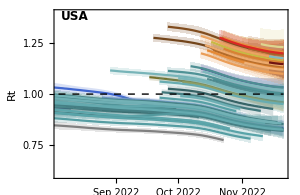
-Graphics- |

```mathematica
fig=Grid[{{countryRtPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt.png

```mathematica
finalRts=Table[If[Length[rtGather["USA",variant]]>0,rtGather["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsLower=Table[If[Length[rtGatherLower["USA",variant]]>0,rtGatherLower["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsUpper=Table[If[Length[rtGatherUpper["USA",variant]]>0,rtGatherUpper["USA",variant][[-1,2]],Null],{variant,variants}];
```

## Prevalence

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{200,100000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,100,200,1000,2000,10000,20000,100000,200000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

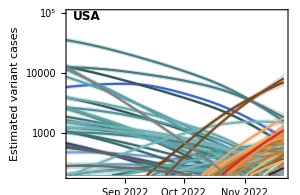
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-log-cases.png

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,32000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

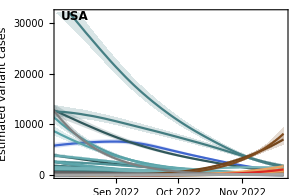
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-cases.png

## Frequency

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
logitTransformDateSeries[dateSeries_]:=Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,dateSeries]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=logitTransformDateSeries[fGather[country,variant]];
lowerSeries=logitTransformDateSeries[fGatherLower[country,variant]];
upperSeries=logitTransformDateSeries[fGatherUpper[country,variant]];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{logitTransform[0.0005],logitTransform[0.9]}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

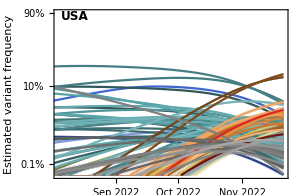
-Graphics- |

```mathematica
fig=Grid[{{countryFrequencyPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-frequency.png

```mathematica
finalFrequencies=Table[fGather["USA",variant][[-1,2]],{variant,variants}];
```

## Rts and frequencies across variants

```mathematica
pos=Flatten[Position[finalRts,x_/;NumberQ[x]]];
```

```mathematica
finalRts=finalRts[[pos]];
```

```mathematica
finalRtsLower=finalRtsLower[[pos]];
```

```mathematica
finalRtsUpper=finalRtsUpper[[pos]];
```

```mathematica
finalFrequencies=finalFrequencies[[pos]];
```

```mathematica
finalVariants=variants[[pos]];
```

```mathematica
finalColors=colors[[pos]];
```

```mathematica
points=ListPlot[Table[{{i,finalRts[[i]]}},{i,Length[finalVariants]}],PlotStyle->finalColors];
```

```mathematica
lines=ListLinePlot[Table[{{i,finalRtsLower[[i]]},{i,finalRtsUpper[[i]]}},{i,Length[finalVariants]}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.35,ImageSize->600,PlotRange->{0.7,1.4},FrameTicks->{{Automatic,Automatic},{Table[{i,Rotate[finalVariants[[i]],Pi/2]},{i,Length[finalVariants]}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]}];
```

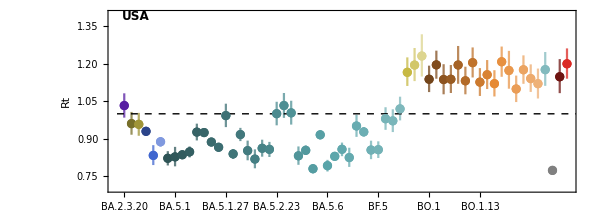

```mathematica
fig=Show[lines,points]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-listplot.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-listplot.png

```mathematica
topPos=Reverse[Ordering[finalRts,-8]];
```

```mathematica
tableValues=Table[{finalVariants[[p]],Round[finalRts[[p]],0.01],ToString[Round[finalRtsLower[[p]],0.01]]<>" - "<>ToString[Round[finalRtsUpper[[p]],0.01]]},{p,topPos}];
```

```mathematica
table=Style[TableForm[tableValues,TableHeadings->{None,{"lineage","Rt estimate","80% uncertainty interval"}},TableSpacing->{3,1}],FontFamily->"Helvetica",FontSize->12];
```

```mathematica
labels=Table[If[MemberQ[topPos,i],finalVariants[[i]],""],{i,Length[finalRts]}];
```

```mathematica
points=ListPlot[MapThread[{{#1,#2}}&,{finalFrequencies,finalRts}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Current lineage frequency","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.65,ImageSize->350,PlotRange->{{0,0.23},{0.7,1.4}},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.05}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]},PlotLabels->Placed[labels,Right]];
```

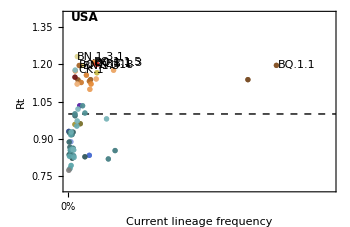
-Graphics- | lineage | Rt estimate | 80% uncertainty interval
BN.1.3.1 | 1.23 | 1.15 - 1.32
BQ.1.1.5 | 1.21 | 1.15 - 1.27
BQ.1.1.3 | 1.21 | 1.15 - 1.27
XBB.1 | 1.2 | 1.14 - 1.26
BQ.1.1 | 1.2 | 1.14 - 1.25
BQ.1.1.18 | 1.2 | 1.12 - 1.27
BN.1.3 | 1.2 | 1.13 - 1.26
CK.1 | 1.18 | 1.11 - 1.25

```mathematica
fig=Grid[{{points,table}}]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-top.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-top.png